# Deutsch-Jozsa algorithm

Show the workings of the Deutsch-Jozsa algorithm

## Example Content

Install and load the QuantumFramework paclet:

```mathematica
PacletInstall["Wolfram/QuantumFramework"]
Needs["Wolfram`QuantumFramework`"]
```

There are four possible boolean functions with one input variable (False, Not, Identity, and True):

```mathematica
Table[ResourceFunction["TruthTable"]@BooleanFunction[k,1],{k,0,3}]
```

{p | False
True | False
False | False,p | !p
True | False
False | True,p | p
True | True
False | False,p | True
True | True
False | True}

Usually one of two quantum encodings are considered for these boolean functions. Phase oracle encodes output bit as a sign flip or phase shift by an angle of π.
Show the corresponding circuits with their action on 0 and 1:

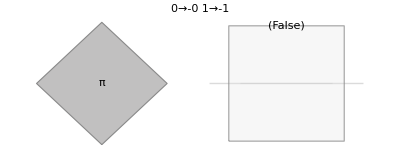
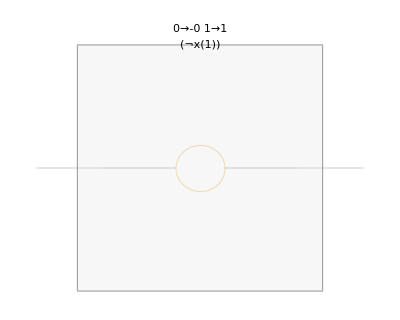
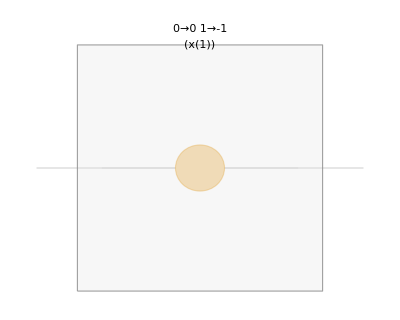
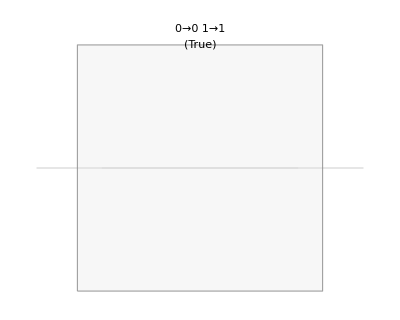

```mathematica
Table[With[{qc=QuantumCircuitOperator[{"DeutschJozsaPhaseOracle",f}]},
qc["Diagram",ImageSize->Tiny,"WireLabels"->None,PlotLabel->Column[Style[#["Formula"]->qc[#],8]&/@{QuantumState["0"],QuantumState["1"]},Frame->All]]
],{f,4}]
```

Constant boolean functions (True and False) correspond to either changing overall global phase by π or doing nothing at all (empty circuit). While balanced functions (half True and half False) are encoded with 0 and 1 operators, which are just convenient names for Pauli Z and -Z.

Another way of encoding these boolean functions is to show more direct bit action with a Boolean oracle representation, which is using an auxiliary qubit initialized to 0 to store its output:

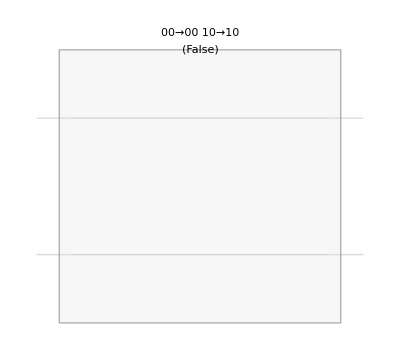
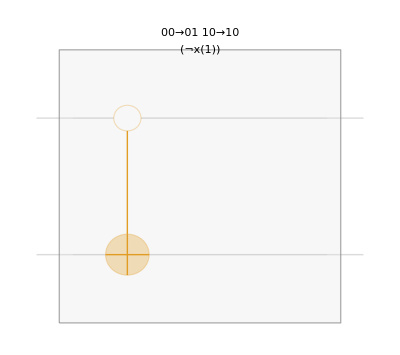
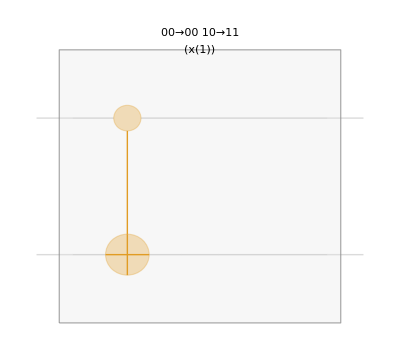
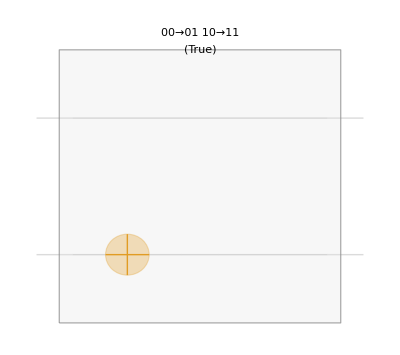

```mathematica
Table[With[{qc=QuantumCircuitOperator[{"DeutschJozsaBooleanOracle",f}]},qc["Diagram",ImageSize->Tiny,"WireLabels"->None,PlotLabel->Column[Style[#["Formula"]->qc[#],8]&/@{QuantumState["00"],QuantumState["10"]},Frame->All]]],{f,4}]
```

Deutsch algorithm is then simply about measuring (in X basis) the result of running such quantum oracle on a uniform superposition as input (+ state):

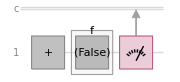
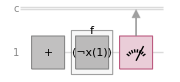
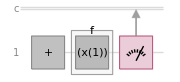
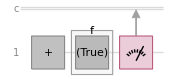

```mathematica
Table[QuantumCircuitOperator[{"+",QuantumCircuitOperator["DeutschJozsaPhaseOracle"[f]],QuantumMeasurementOperator["X"]}]["Diagram",ImageSize->Small],{f,4}]
```

Boolean oracle version also requires phase shifting initial output qubit by π, so that it is initialized as - instead:

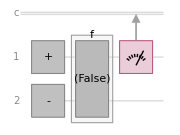
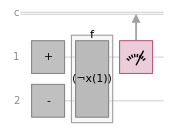
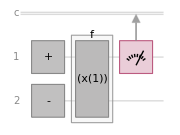
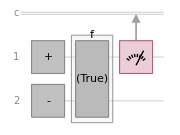

```mathematica
Table[QuantumCircuitOperator[{"+","-"->2,QuantumCircuitOperator["DeutschJozsaBooleanOracle"[f]],QuantumMeasurementOperator["X"]}]["Diagram",ImageSize->Small],{f,4}]
```

Or use built-in circuits with random oracle as a default:

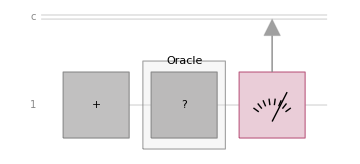

```mathematica
QuantumCircuitOperator["DeutschPhase"]
```

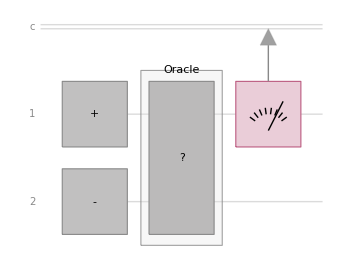

```mathematica
QuantumCircuitOperator["Deutsch"]
```

Then with certainty outcome +/𝓍_+ means that oracle is a constant function, while -/𝓍_- means it's a balanced one:

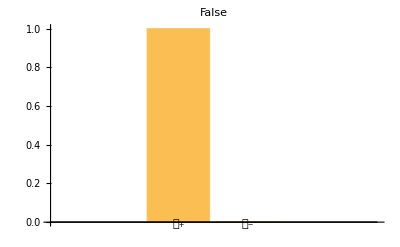
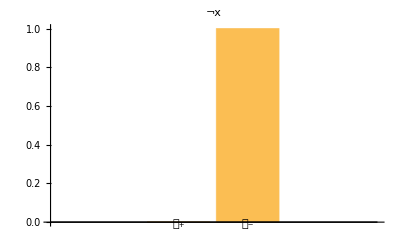
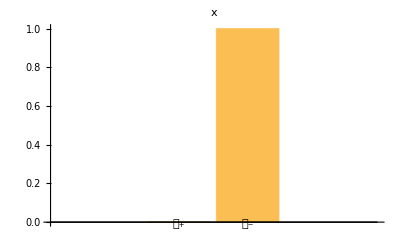
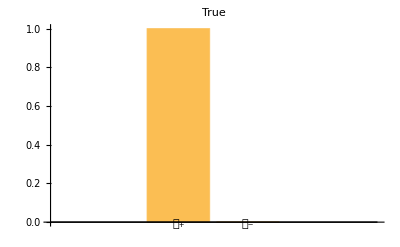

```mathematica
Table[Show[QuantumCircuitOperator[{"Deutsch",f}][]["ProbabilityPlot"],PlotLabel->BooleanConvert[BooleanFunction[f-1,1]][x],ImageSize->Tiny],{f,4}]
```

If one has more than one variable then the exact same procedure is called Deutsch-Josza algorithm. For example for two variables these are the corresponding Phase and Boolean oracles:

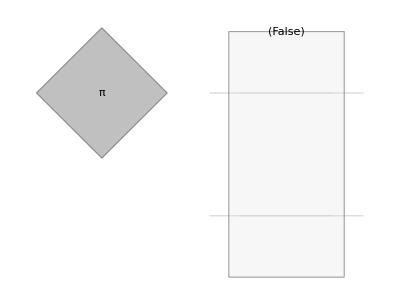
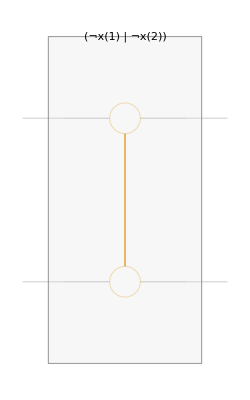
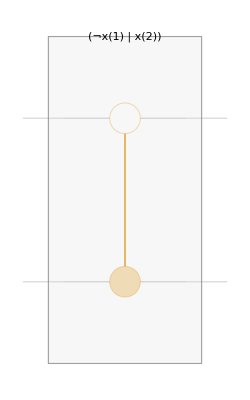
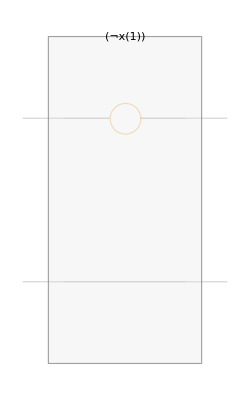
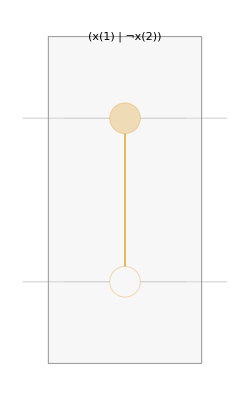
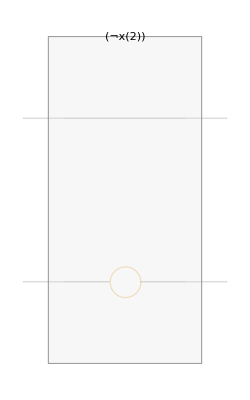
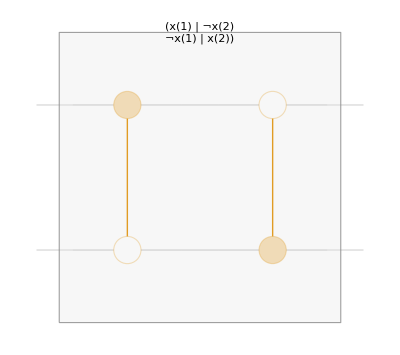
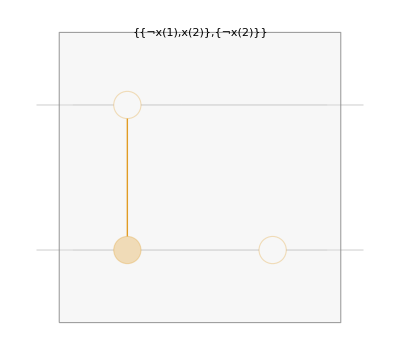

```mathematica
Table[QuantumCircuitOperator[{"DeutschJozsaPhaseOracle",f,2}]["Diagram",ImageSize->Tiny,"WireLabels"->None],{f,16}]
```

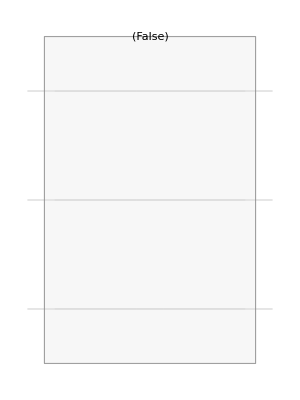
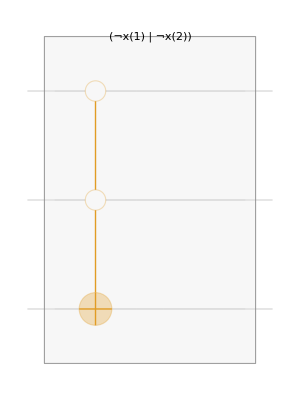
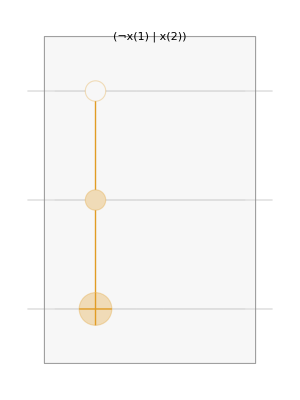
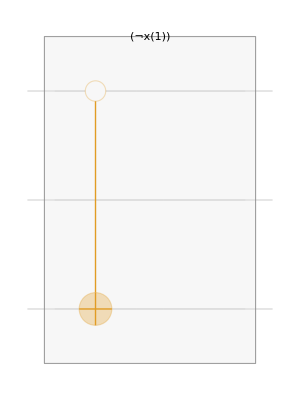
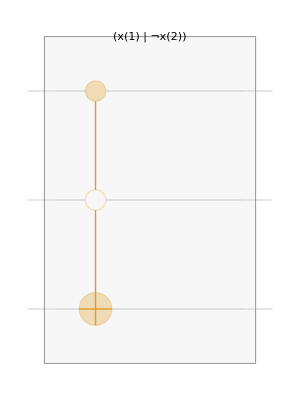
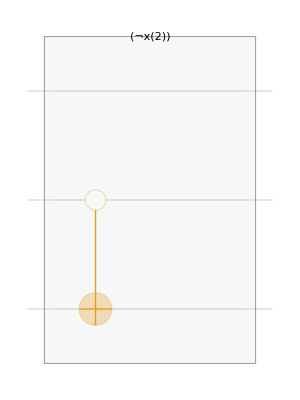
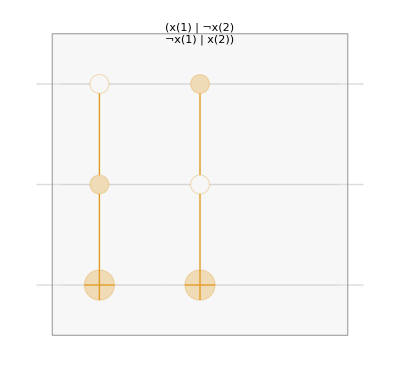
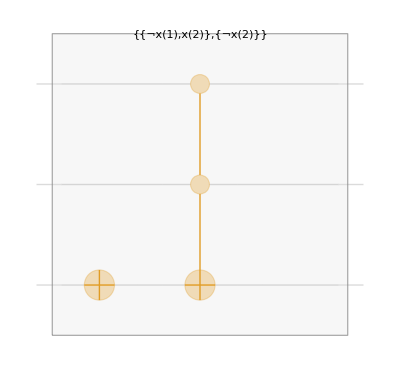

```mathematica
Table[QuantumCircuitOperator[{"DeutschJozsaBooleanOracle",f,2}]["Diagram",ImageSize->Tiny,"WireLabels"->None],{f,16}]
```

With measurement now being done on two qubits:

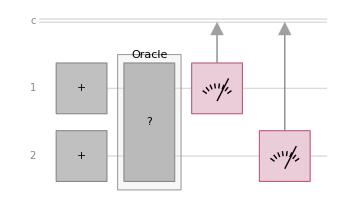

```mathematica
QuantumCircuitOperator[{"DeutschJozsaPhase",Automatic,2}]
```

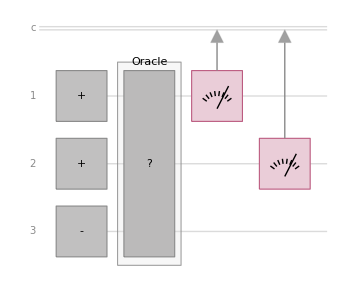

```mathematica
QuantumCircuitOperator[{"DeutschJozsa",Automatic,2}]
```

There are not just constant and balanced functions now, but also unbalanced ones, about which the algorithm can't says anything at all:

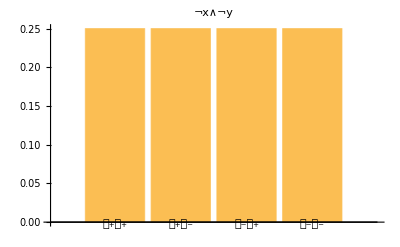
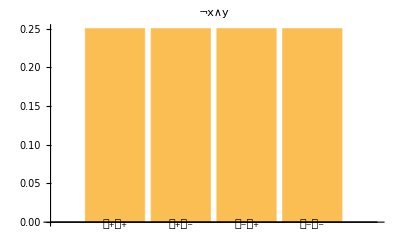
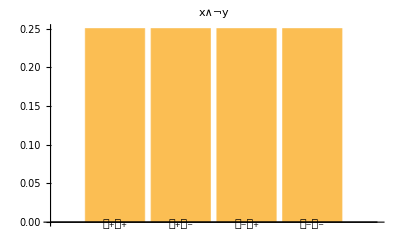
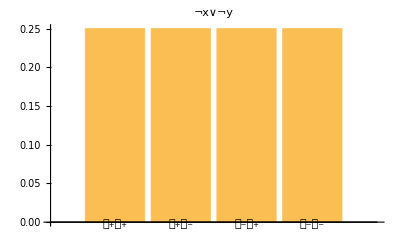
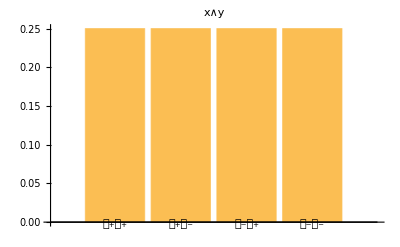
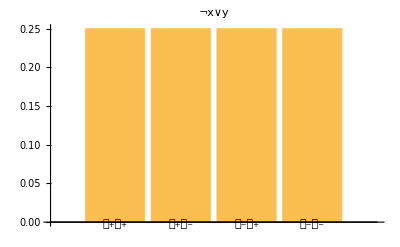
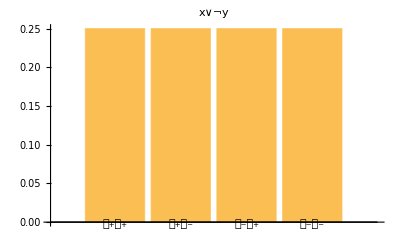
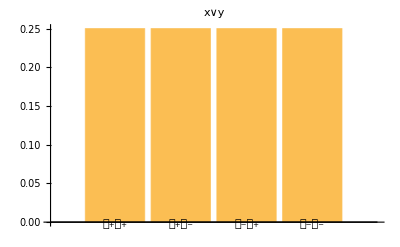

```mathematica
Table[With[{bf=BooleanFunction[f-1,2]},If[Equal@@Counts[BooleanTable[bf]],
Nothing,
Show[QuantumCircuitOperator[{"DeutschJozsaPhase",f,2}][]["ProbabilityPlot"],PlotLabel->BooleanConvert[bf][x,y]]
]],{f,16}]
```

But constant function similarly to the single variable case produces ++ with certainty, while balanced function does not, so one can again determine whether an oracle is constant or balanced with a single run of the experiment:

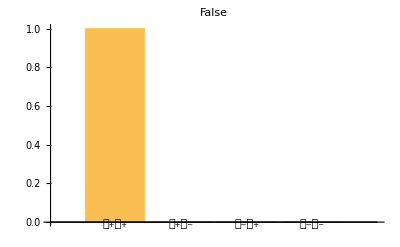
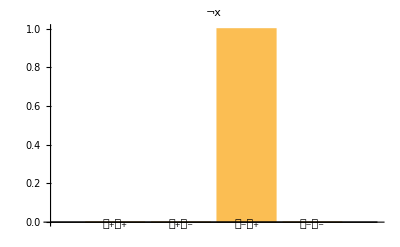
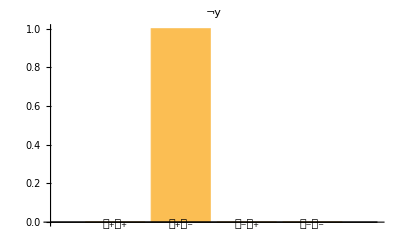
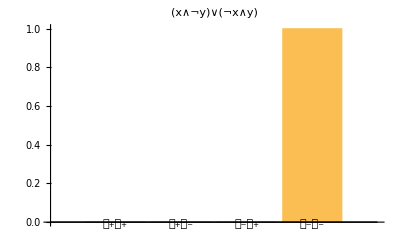
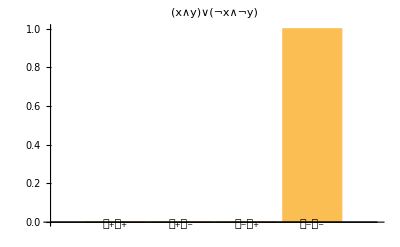
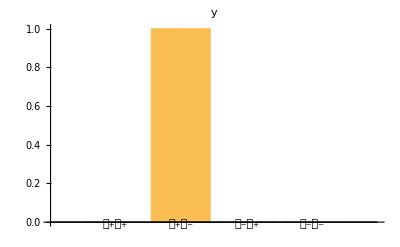
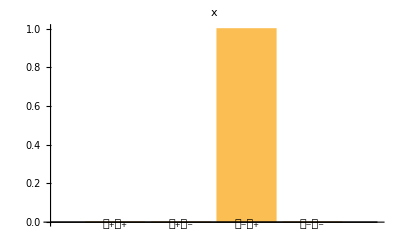
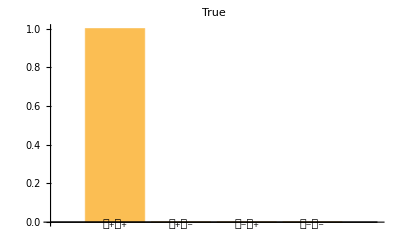

```mathematica
Table[With[{bf=BooleanFunction[f-1,2]},If[Equal@@Counts[BooleanTable[bf]],
Show[QuantumCircuitOperator[{"DeutschJozsaPhase",f,2}][]["ProbabilityPlot"],PlotLabel->BooleanConvert[bf][x,y]],
Nothing
]],{f,16}]
```

## Supporting Data and Definitions

(Your data can be Dataset[…], EntityStore[…], Image[…], Audio[…] or any other expression)

(xxxx can be your data, or File[…], CloudObject[…] or LocalObject[…] that contains it.)

## Thumbnail Image

```mathematica
QuantumCircuitOperator["DeutschPhase"]["Diagram"]
```

-Graphics-

## Source & Additional Information

### Contributed By

Wolfram Research, Quantum Computation Framework Team

### Keywords

quantum

algorithm

oracle

function

### Categories

Algebra
 Calculus
 Complex Systems
 Control Systems
 Engineering
 Food & Nutrition
 Graphs & Networks
 Machine Learning
 Optimization
 Puzzles and Recreation
 Social Sciences
 Time-Related Computation
  |  Astronomy
 Cellular Automata
 Computer Science
 Creative Arts
 Finance & Economics
 Geography
 Image Processing
 Mathematics
 Physics
 Quantum Computation
 System Modeling
 Video Processing
 |  Audio Processing
 Chemistry
 Computer Vision
 Data Science
 Finite Element Method
 Geometry
 Life Sciences
 Notebooks & User Interfaces
 Presentation & Publication
 Signal Processing
 Text & Language Processing
 Visualization & Graphics

### Related Documentation Pages

Symbol name or documentation URI

### Related Resource Objects

Wolfram/QuantumFramework

Example: Grover's Search Algorithm

### Original Source References and Attributions

Source, reference or citation

### Links

QuantumFramework | Wolfram Language Paclet Repository

### Compatibility

#### Wolfram Language Version

13.2+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

## Author Notes

Additional information about limitations, issues, etc.